# μLang — Computationally Generating a Morphologically Average Conlang Lexicon from Multilingual Translations

Constructed languages, or conlangs, are languages that were artificially created instead of being naturally evolved over several generations. A crucial part of every conlang is the lexicon — the vocabulary. While most lexicons are generated manually or through the help of randomized selection, I present several methods to generating a quantitatively “average” lexicon, that is, generating new words that may have similar features, spelling, or pronunciation compared to several translations of the same word in different languages.

## Initial Setup

I start with a simple word and and using translations provided by the Wolfram Language. In this case, I’m using “sun.”

```mathematica
KEYWORD = "sun";
```

Get the top 35 most spoken languages

```mathematica
languages=EntityClass["Language",{"TotalSpeakers"->TakeLargest[35]}]//EntityList
```

{Chinese,English,Mandarin Chinese,Hindi,Arabic,Spanish,French,Standard Arabic,Bengali,Russian,Portuguese,Malay,Indonesian,Urdu,German,Japanese,Lahnda,Swahili,Swahili,Marathi,Telugu,Turkish,Yue Chinese,Tamil,Western Panjabi,Wu Chinese,Korean,Vietnamese,Hausa,Javanese,Egyptian Arabic,Italian,Persian,Gujarati,Thai}

Get raw translations of “sun” to the determined languages

```mathematica
rawTranslations = KeyValueMap[#1->First[#2]&,WordTranslation[KEYWORD, languages]];
rawTranslations//Short
```

{Chinese→太陽,English→sun,Mandarin Chinese→太陽,Hindi→सूर्य,Arabic→شَمس,Spanish→sol,French→soleil,Standard Arabic→NotAvailable,Bengali→সূর্য্য,Russian→солнце,Portuguese→sol,Malay→NotAvailable,Indonesian→matahari,Urdu→سورج,German→Sonne,Japanese→日,Lahnda→NotAvailable,Swahili→N…le,Swahili→jua,Marathi→सूर्य,Telugu→నూర్యుడు,Turkish→güneş,Yue Chinese→太阳,Tamil→கதிரவன்,Western Panjabi→NotAvailable,Wu Chinese→NotAvailable,Korean→태양,Vietnamese→mặt trời,Hausa→rana,Javanese→srengenge,Egyptian Arabic→NotAvailable,Italian→sole,Persian→NotAvailable,Gujarati→સૂર્ય,Thai→พระอาทิตย์}

Standardize all translated words — Transliterate to the Roman alphabet and ensure all words are lowercase

```mathematica
translatedList=DeleteCases[DeleteDuplicates[ToLowerCase[Select[Transliterate[Values[rawTranslations]],StringMatchQ[#,CharacterRange["A","z"]..]&]]], "notavailable"]
```

{sun,surya,shams,sol,soleil,suryya,solnce,matahari,swrj,sonne,ri,jua,nuryudu,gunes,katiravan,taeyang,rana,srengenge,sole,phraxathity}

## Most Common Letter

Naturally, this is the very first idea I jumped to. I counted the most frequent letter at every index, found the average length of the original words, and concatenated the most common letters together.

Split each word into a List of characters

```mathematica
charLists = Characters /@ translatedList;
charLists//Short
```

{{s,u,n},{s,u,r,y,a},{s,h,a,m,s},{s,o,l},{s,o,l,e,i,l},{s,u,r,y,y,a},{s,o,l,n,c,e},«7»,{k,a,t,i,r,a,v,a,n},{t,a,e,y,a,n,g},{r,a,n,a},{s,r,e,n,g,e,n,g,e},{s,o,l,e},{p,h,r,a,x,a,t,h,i,t,y}}

Find the average length of all words

```mathematica
avgLen=Round[Mean[Length/@charLists]]
```

6

For words shorter in length than the average length, pad the List with dashes. For words longer than the average length, truncate the List accordingly.

```mathematica
augmentedLists=Map[Function[chars,If[Length[chars]>avgLen,Take[chars,avgLen],PadRight[chars,avgLen,"-"]]],charLists];
augmentedLists//Short
```

{{s,u,n,-,-,-},{s,u,r,y,a,-},{s,h,a,m,s,-},{s,o,l,-,-,-},{s,o,l,e,i,l},{s,u,r,y,y,a},{s,o,l,n,c,e},«7»,{k,a,t,i,r,a},{t,a,e,y,a,n},{r,a,n,a,-,-},{s,r,e,n,g,e},{s,o,l,e,-,-},{p,h,r,a,x,a}}

Transpose the charList for easier calculation of the most frequent character at every position

```mathematica
transposed=Transpose[augmentedLists];
```

Find the most frequency character at each position and generate the average word

```mathematica
mostFreqChar=Map[Function[col,Module[{counts,filtered},filtered=DeleteCases[col,"-"];If[filtered==={},"-",counts=Tally[filtered];
First@First@SortBy[counts,-Last[#]&]]]],transposed];
```

```mathematica
mostFreqCharWord=StringJoin[DeleteCases[mostFreqChar,"-"]]
```

suryaa

While this method does “work,” it is rather boring. It always produces one very predictable word and isn’t very creative. To generate an exciting lexicon, I explored some other methods.

## Most Common Digram

My seconnd approach  was to split each word into digrams (pairs of consecutive letters) and find the most common digram in each position. Then, we can join the most common digrams together. For example, “su” is the first digram in “sun” and “un” is the second digram in “sun.”

Calculate the average syllable count

```mathematica
SYLLABLECOUNT = Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]]
```

2

Split each word into digrams and record the position of each digram.

```mathematica
positionedDigrams=Flatten[Table[If[StringLength[word]>=pos+1,{pos,StringTake[word,{pos,pos+1}]},Nothing],{word,translatedList},{pos,StringLength[word]-1}],1];
positionedDigrams//Short
```

{{1,su},{2,un},{1,su},{2,ur},{3,ry},{4,ya},{1,sh},{2,ha},{3,am},{4,ms},{1,so},{2,ol},{1,so},{2,ol},{3,le},{4,ei},{5,il},{1,su},{2,ur},«54»,{3,en},{4,ng},{5,ge},{6,en},{7,ng},{8,ge},{1,so},{2,ol},{3,le},{1,ph},{2,hr},{3,ra},{4,ax},{5,xa},{6,at},{7,th},{8,hi},{9,it},{10,ty}}

Group digrams by their position

```mathematica
groupedByPosition=GroupBy[positionedDigrams,First->Last];
Iconize[groupedByPosition]
```

Count the frequency of each digram in each position

```mathematica
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
countsByPosition//First
```

<|su→3,sh→1,so→5,ma→1,sw→1,ri→1,ju→1,nu→1,gu→1,ka→1,ta→1,ra→1,sr→1,ph→1|>

Get the most frequent digram in each position

```mathematica
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[1]],{pos,Sort@Keys[countsByPosition]}]
```

{{so},{ol},{ry},{ya},{il},{ar},{ri},{an},{it},{ty}}

Generate new words by combining the most frequent digrams

```mathematica
generateWord[]:=Module[{numSyllables,selectedLists,syllables},numSyllables:=RandomInteger[{Max[1, SYLLABLECOUNT-2], Min[Length[topDigramsByPosition], SYLLABLECOUNT+2]}];
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]]

mostDigramGenerated=DeleteDuplicates[Table[generateWord[],{10}]]
```

{soolry,soolryya,sool,so}

This isn’t great either. While there are some pronounceable words, this method is very basic and relies on the most common digrams. In fact, both of the previous methods relied very strictly on the most frequent characters with extremely basic substitution algorithms.

## Genetic Evolution

A different approach is to imagine the original list of translated words as a base “population.” Through a genetic algorithm, we can “evolve” the population and generate new words that are similar but completely unique. A genetic algorithm has a few parts:

Population: This is a set of possible solutions. In this case, the population is a List of possible “average” words. We will generate the starting population by randomly combining digrams from the original word list. Then, we will evolve the population.

Fitness: This a function that evaluates how “good” any individual is. Our fitness metric will measure how similar an individual is to the starting word list.

Selection: We want to select the top n most fit individuals to continue into the next population

Recombination: We can combine two “parents”, or parts of two words from a generation to form a “child” for the succeeding generation. We use one-point and two-point crossover.

Mutation: Each generation, we randomly alter some words to simulate random genetic mutation. This introduces more variability in the population and allows the population to explore a greater breadth of possibilities. We will randomly replace a letter or digram in some  randomly chosen words.

Define important variables. populationSize is the size of the population each generation and mutationRate

```mathematica
Clear[populationSize, generations, mutationRate, topDigramsByPosition, fitnessFunction, population, randomString, allBest];
populationSize=100;
generations=500;
mutationRate=0.05;
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[5]],{pos,Sort@Keys[countsByPosition]}]
allBest = {};
```

{{so,su,sh,ma,sw},{ol,ur,un,at,ha},{ry,le,am,ln,ta},{ya,ms,ei,yy,nc},{il,ya,ce,ha,ud},{ar,du,av,ng,en},{ri,va,ng,th},{an,ge,hi},{it},{ty}}

```mathematica
words = translatedList;
charSet = Flatten[topDigramsByPosition];
MAXLENGTH = Round[Mean[StringLength/@ words]]
```

6

Our fitness function will calculate the average Levenshtein distance between a candidate word and each word in the original word list

```mathematica
fitnessFunction[candidate_String]:=Module[{maxDistance},
  maxDistance=Max[EditDistance[candidate,#] & /@ words];
  1-N[Mean[EditDistance[candidate,#] & /@ words]/maxDistance]
]
```

The fitness of a word similar to possible KEYWORD translations is significantly greater than a completely unrelated fitness word

```mathematica
fitnessFunction[WordTranslation[KEYWORD, "Spanish"][[1]]]
```

0.577273

```mathematica
fitnessFunction["random word"]
```

0.0909091

Here is our list of possible digrams

```mathematica
charSet
```

{so,su,sh,ma,sw,ol,ur,un,at,ha,ry,le,am,ln,ta,ya,ms,ei,yy,nc,il,ya,ce,ha,ud,ar,du,av,ng,en,ri,va,ng,th,an,ge,hi,it,ty}

Create our original population by randomly combining digrams

```mathematica
randomString[]:=StringJoin@RandomChoice[Flatten[topDigramsByPosition],RandomInteger[{SYLLABLECOUNT,SYLLABLECOUNT+2}]];
Print["Initial population--"];
population=Table[randomString[],{populationSize}]
```

Initial population--

{yatyeihi,ngdu,mahaha,swya,sule,duurng,ngit,tyryolty,lnsomahi,urdu,tayy,ilcece,shunmsei,soolry,ryeiar,ngatsh,ryenamry,ududthhi,hacedule,ncngsu,unlehaur,duyaya,swhihi,riilhasu,ngln,udlnamri,enhianri,taenty,yalnyy,vahayy,vadums,hage,taun,yaha,aram,ceunhiry,haatil,hiso,maei,olswng,ncei,maud,risuyy,ilsu,ilyyya,yayysw,uditncma,sule,shth,sungryil,lethhi,hitasohi,ncavsh,anryngso,hahaln,tyit,shsu,lnduatya,yamang,lnma,lnav,hishma,anmaitge,yalnenam,udit,msurgeyy,cerihi,yyngnc,hahary,haat,yamaln,ryyyce,oludatav,enatgeng,lnarmsnc,amam,soyageud,swryya,yyncitan,thsoyy,ncnc,vamaarth,ilhi,ilatry,atsh,nglnud,uratamsu,ceswav,thmsha,ceya,amrileth,soty,eincsohi,maun,olngryth,lety,cethanur,leunnghi,song,shng}

With everything set up, I can simulate several hundred generations of evolution. I implemented one-point, two-point, and length-varied two-point crossover. One-point crossover

```mathematica
onePointCrossover[p1_,p2_]:=Module[{len,chars1,chars2},len=Min[StringLength[p1],StringLength[p2]];
chars1=Characters[p1];
chars2=Characters[p2];
StringJoin@Table[RandomChoice[{chars1[[i]],chars2[[i]]}],{i,1,len}]];

twoPointCrossover[p1_,p2_]:=Module[{len,pt1,pt2,c1,c2},len=Min[StringLength[p1],StringLength[p2]];
{pt1,pt2}=Sort@RandomSample[Range[len],2];
c1=Characters[p1];
c2=Characters[p2];
StringJoin@Join[Take[c1,pt1-2],Take[c2,{pt1,pt2}],Drop[c1,pt2]]];

lengthVaryTwoPointCrossover[p1_,p2_]:=Module[{len1,len2,minLen,pt1,pt2,c1,c2,child},len1=StringLength[p1];
len2=StringLength[p2];
minLen=Min[len1,len2];
{pt1,pt2}=Sort@RandomSample[Range[minLen],2];
c1=Characters[p1];
c2=Characters[p2];
child=Join[Take[c1,pt1-1],Take[c2,{pt1,pt2}],Drop[c1,pt2]];
If[Length[child]>MAXLENGTH,child=Take[child,MAXLENGTH]];
StringJoin[child]];

mutate[str_]:=StringJoin@Table[If[RandomReal[]<mutationRate,RandomChoice[charSet],c],{c,Characters[str]}];
```

```mathematica
allBest=Table[fitnesses=fitnessFunction/@population;
bestCandidate=population[[First@Ordering[fitnesses,-1]]];
parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
population=Table[mutate@lengthVaryTwoPointCrossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];
bestCandidate,
{gen,1,generations}
];

bestWord=First@MaximalBy[allBest,fitnessFunction];
Print["Best word found: ",bestWord];
Print["Fitness: ",fitnessFunction[bestWord]];
```

Best word found: sune

Fitness: 0.604545

```mathematica
allBest//Short
```

{sule,song,sone,sung,suln,sune,sunn,suln,suln,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,«449»,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune,sune}

```mathematica
allBestFitnesses = fitnessFunction[#]&/@ allBest;
allBestFitnesses//Short
```

{0.590909,0.581818,0.6,0.586364,0.590909,0.604545,0.590909,0.590909,0.590909,«482»,0.604545,0.604545,0.604545,0.604545,0.604545,0.604545,0.604545,0.604545,0.604545}

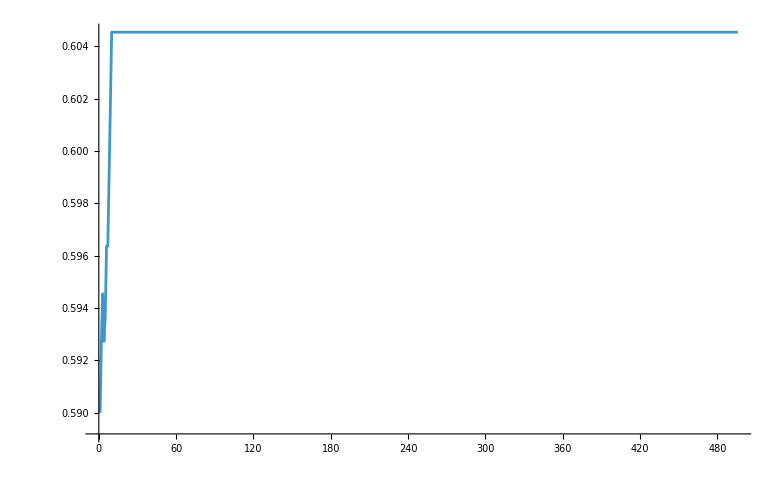

```mathematica
ListLinePlot[MovingAverage[allBestFitnesses, 5]]
```

## Viewing this as an optimization problem

We can view evolution also as an optimization problem. We want to continuously evolve a string to be have the lowest average edit distance to all the multilingual words. We take a string and evolve it through several hundred generations. Each generation, we find the word that is farthest away (in Levenshtein Distance) to the evolving string. Then, we change one character in the evolving string to match a character in the most distant word. Over hundreds of generations, the evolving string takes on features of all the multilingual words.

```mathematica
Clear[baseWord, testList, padChar, baseWordStates, targetWords,GENERATIONS];
baseWord=StringJoin@RandomChoice[CharacterRange["a", "z"], 5]
startingWord = baseWord;
(*testList=ToLowerCase[Transliterate[{WordTranslation[KEYWORD,"Spanish"][[1]],WordTranslation[KEYWORD,"English"][[1]],WordTranslation[KEYWORD,"Portuguese"][[1]],WordTranslation[KEYWORD,"Romanian"][[1]],WordTranslation[KEYWORD,"Galician"][[1]],WordTranslation[KEYWORD,"Italian"][[1]], WordTranslation[KEYWORD,"French"][[1]], WordTranslation[KEYWORD, "Catalan"][[1]]}]]*)
testList=translatedList
padChar="_";
baseWordStates={baseWord};
targetWords={};
GENERATIONS=400;
```

djdhj

{sun,surya,shams,sol,soleil,suryya,solnce,matahari,swrj,sonne,ri,jua,nuryudu,gunes,katiravan,taeyang,rana,srengenge,sole,phraxathity}

```mathematica
normalizeFrequencies[calculateCharFrequencies[testList]]
```

normalizeFrequencies[calculateCharFrequencies[{sun,surya,shams,sol,soleil,suryya,solnce,matahari,swrj,sonne,ri,jua,nuryudu,gunes,katiravan,taeyang,rana,srengenge,sole,phraxathity}]]

```mathematica
calculateCharFrequencies[wordList_]:=Module[{maxLen,paddedWords,freqTables},maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
freqTables=Table[Counts[StringTake[#,{pos}]&/@paddedWords],{pos,1,maxLen}];
freqTables];

normalizeFrequencies[freqTable_]:=Module[{nonZeroEntries,total},
nonZeroEntries=Select[freqTable,#>0&];
total=Total[Values[nonZeroEntries]];
If[total==0,freqTable,Association[#->If[freqTable[#]>0,N[freqTable[#]/total],0]&/@Keys[freqTable]]]];

getAllChars[wordList_]:=Module[{maxLen,paddedWords,allChars},maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
allChars=Union[Flatten[Characters/@paddedWords]];
allChars];

allPossibleChars=getAllChars[testList];
rawFrequencies=calculateCharFrequencies[testList];

charFreqWeights=Table[Module[{posFreq,normalizedFreq},posFreq=rawFrequencies[[i]];
Do[If[!KeyExistsQ[posFreq,char],posFreq[char]=0],{char,allPossibleChars}];
normalizeFrequencies[posFreq]],{i,1,Length[rawFrequencies]}];

pad[w1_,w2_]:=Module[{maxLen,p1,p2},maxLen=Max[StringLength[w1],StringLength[w2]];
{StringPadRight[w1,maxLen,padChar],StringPadRight[w2,maxLen,padChar]}];

wordDifference[w1_,w2_]:=EditDistance[Pad[w1, w2][[1]], Pad[w1, w2][[2]]];

mostDifferentWord[base_,list_]:=Module[{diffs},diffs=Table[{word,wordDifference[base,word]},{word,list}];
First@MaximalBy[diffs,Last]];

findDifferingIndices[str1_,str2_]:=Module[{minLen,diffs},minLen=Min[StringLength[str1],StringLength[str2]];
diffs=Select[Range[minLen],StringTake[str1,{#}]=!=StringTake[str2,{#}]&];
diffs]

evolveToward[base_,target_]:=Module[{basePadded,targetPadded,diffIndices,i},
{basePadded, targetPadded} = pad[base, target];
diffIndices=findDifferingIndices[basePadded, targetPadded];
If[
diffIndices==={},
basePadded,
i=RandomChoice[diffIndices];
basePadded=StringReplacePart[basePadded,Part[Characters[targetPadded], i],{i,i}];basePadded
]
];

weightedRandomTarget[base_,list_]:=Module[{diffs,total,weights},
diffs=Table[{word,wordDifference[base,word]},{word,list}];
total=Total[diffs[[All,2]]];
If[total==0,

RandomChoice[list],
weights=(diffs[[All,2]]^3)/Total[diffs[[All,2]]^3];
RandomChoice[weights->diffs[[All,1]]]]
];

randomMutation[word_,rate_:0.05]:=Module[{chars,mutated},chars=Characters[word];
mutated=Map[If[RandomReal[]<rate,RandomChoice[CharacterRange["a","z"]~Join~{padChar}],#]&,chars];
StringJoin[mutated]];

layoutTestWords[baseWord_,testList_]:=Module[{angles,positions,dist,x,y},angles=Subdivide[0,2*Pi,Length[testList]][[1;;-2]];
positions={};
Do[dist=wordDifference[baseWord,testList[[i]]];
x=Cos[angles[[i]]]*dist;
y=Sin[angles[[i]]]*dist;
AppendTo[positions,{testList[[i]],x,y}],{i,1,Length[testList]}];
positions];


evolveTowardWeighted[base_,target_]:=Module[{basePadded,targetPadded,diffIndices,i,targetChar,baseChar,weight},{basePadded,targetPadded}=pad[base,target];
diffIndices=findDifferingIndices[basePadded,targetPadded];
If[diffIndices==={},basePadded,
i=RandomChoice[diffIndices];
targetChar=StringTake[targetPadded,{i,i}];
baseChar=StringTake[basePadded,{i,i}];
weight=
If[
i<=Length[charFreqWeights],
chars=Keys[charFreqWeights[[i]]];
weights = Values[charFreqWeights[[i]]];
choice = RandomChoice[weights->chars];
StringReplacePart[basePadded, choice, {i, i}], basePadded]]];

evolutionData={};
baseWordStates={baseWord};
targetWords={};
optimalWordSoFar=baseWord;
optimalDistance=Mean[wordDifference[baseWord,#]&/@testList];

Do[target=weightedRandomTarget[baseWord,testList];
AppendTo[targetWords,target];
baseWord=evolveTowardWeighted[baseWord,target];
(*baseWord=randomMutation[baseWord,0.1];*)
AppendTo[baseWordStates,baseWord];
currentDistance=Mean[wordDifference[baseWord,#]&/@testList];
If[currentDistance<optimalDistance,optimalWordSoFar=baseWord;
optimalDistance=currentDistance;];,
{gen,1,GENERATIONS}
];

testPositions=layoutTestWords[baseWordStates[[1]],testList];
positionDict=Association[#[[1]]->{#[[2]],#[[3]]}&/@testPositions];
```

```mathematica
createEvolutionAnimation[]:=Module[{frames,maxFrames,basePos={0,0},targetPos,newX,newY,t=0.25},maxFrames=Length[baseWordStates];
frames=Table[Module[{currentWord,target,bx,by,tx,ty,optimalWord},
currentWord=baseWordStates[[frame]];
optimalWord=First[MinimalBy[baseWordStates,wordDifference[currentWord,#]&]];
If[frame<=Length[targetWords],target=targetWords[[frame]],target=targetWords[[-1]]];
targetPos=positionDict[target];
tx=targetPos[[1]];
ty=targetPos[[2]];
If[frame==1,{bx,by}={0,0},newX=basePos[[1]]+t*(tx-basePos[[1]]);
newY=basePos[[2]]+t*(ty-basePos[[2]]);
basePos={newX,newY};
{bx,by}=basePos;];
Show[Graphics[{Gray,Table[Text[Style[StringReplace[testPositions[[i,1]],"_"->""],FontSize->12],{testPositions[[i,2]],testPositions[[i,3]]}],{i,1,Length[testPositions]}],Red,Thickness[0.01],Line[{{bx,by},{tx,ty}}],Red,Text[Style[StringReplace[currentWord,"_"->""],FontSize->18,Bold],{bx,by}],Red,Text[Style["Target: "<>StringReplace[target,"_"->""],FontSize->12],{0,9.5}],Blue}],PlotRange->{{-10,10},{-10,10}},Axes->False,Frame->False,ImageSize->{400,400}]],{frame,1,maxFrames}];
ListAnimate[frames,AnimationRate->5,AnimationRepetitions->1]];

evolutionAnimation=createEvolutionAnimation[];
evolutionAnimation
```

```mathematica
StringReplace[#, "_"->""]&/@baseWordStates
```

{djdhj,djlhj,djlmj,djamj,djamh,djamg,djamu,tjamu,rjamu,rjame,rjams,sjams,sjays,sjlys,sjlys,solys,solyy,solyy,solyy,shlyy,shlys,shlys,shlyy,shlyh,salyh,saljh,suljh,suljx,sunjx,sanjx,sanjx,sanex,swnex,swne,swned,swned,swted,swtid,swted,swtea,sutea,sute,sutea,sotea,rotea,roteha,rotehn,roten,roten,roten,rolen,solen,soleny,shleny,shley,shlny,shln,srln,srln,srln,srlne,srene,suene,sueme,sueje,suee,suea,swea,swna,sona,sona,sona,sona,sona,sana,sana,rana,sana,sanya,sany,sani,shni,shni,shng,shng,shrg,shag,shng,shn,sun,sue,soe,noe,noee,nhee,naee,naey,maey,maey,maly,saly,saay,saaye,saayl,sanyl,sanyl,sanyl,sany,sanye,sanye,sanyn,sanan,sanacn,sanacn,saracn,soracn,soracn,soracn,sorycn,sonycn,sonyca,sonyc,soryc,sory,sory,sori,suri,siri,siri,sir,swr,sur,sur,surm,surm,sorm,sorj,sorj,sorm,sore,sore,shre,shre,shre,shne,shnex,shnex,shnes,shnys,shnys,shns,shns,shns,suns,sans,sany,sany,sary,say,say,saye,saya,sarya,sarya,sarca,sarya,surya,sunya,sunua,sunua,sunga,sunaa,sunaa,suniaa,guniaa,guniaa,gunia,gonia,goeia,goeya,roeya,poeya,poeya,poeya,roeya,roeya,roeyag,roeyaag,roryaag,roryaag,roryaag,roryaeg,toryaeg,toryaeg,roryaeg,roraaeg,roraaeg,roraaeg,soraaeg,soraae,soraxe,soraxer,suraxer,saraxer,saraxer,saraser,sanaser,sanaser,sanase,sanasa,sunasa,sonasa,nonasa,nonnsa,nonns,nolns,nalns,nalis,nanis,nanisi,nanisi,narisi,nalisi,nalisvi,nanisvi,nanisvi,nannsvi,kannsvi,kannsi,kanns,kalns,kulns,kulnu,kulnu,kulna,kulnaa,kulna,kulna,kulna,kulya,kulya,kulya,kulya,kulya,kulaa,kulah,sulah,sulahn,sulaxn,sulaxen,sulaxen,sulahen,sulahe,sulahe,sulae,sulan,swlan,swtan,swten,swtein,swlein,swlen,swlen,swlea,sweea,sieea,rieea,rieea,rueea,rueea,rueya,ruey,ruey,ruey,ruej,runj,ranj,rany,rony,sony,sony,suny,tuny,kuny,kuny,kunyy,kueyy,kueny,kueay,kueay,kueay,rueay,roeay,soeay,soea,soeas,sueas,sues,suesu,sueu,sueu,suenu,sutnu,sutn,sutn,sutn,suen,sue,sue,sun,sun,sin,sinj,sinj,sirj,sorj,sore,sore,sone,sony,sony,sany,sany,sany,sany,saly,saly,saln,soln,soln,soln,sorn,sonn,sorn,surn,surn,sury,sury,sury,sury,sury,surya,suryh,siryh,siryh,sieyh,sieys,saeys,saeyg,sueyg,sueys,sueys,suey,suey,sury,sury,suty,sutyu,sunyu,sunyu,sunju,sunjs,sunjs,suejs,suejsn,surjsn,suejsn,suesn,saesn,saeysn,saeysn,paeysn,paeyhn,paeyh,saeyh,saeyh,saryh,saryhl,sarahl,saragl,saragl,saraga,sarag,saraa,suraa,kuraa,kuray,kuraa,kuraa,kurja,kurjx,kutjx,kutjx,rutjx,rutjxg,rutjg,rutjg,rutjg,gutjg,gutjg,gutjg}

```mathematica
StringReplace[Last@baseWordStates,"_"->""]
```

gutjg

## Generation with Neural Net Features

A more modern approach may be to take advantage of neural net embeddings. A neural net/deep learning model encodes words in a numeric representation called embeddings or feature vectors. For text, embeddings usually encode semantic meaning. We can ask the neural net to generate new words with similar embedding values as the training set (the original word list), generating new but similar words.

```mathematica
net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"]
```

NetGraph[…]

```mathematica
vocabulary=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
```

```mathematica
net=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]]
```

NetGraph[…]

```mathematica
results = 
 NetTrain[net, <|"Input" -> translatedList|>, All, LossFunction -> "Loss", 
  MaxTrainingRounds ->500]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:500  rounds:500  time:15s  examples/s:681
data | ,,  training examples:20  processed examples:10000  skipped examples:0
method | ,,  ADAMoptimizer  batch size20CPU
round | ,,  loss:5.22×10^-1  error:20.7%
 | 
 | ]

```mathematica
trainednet=results["TrainedNet"];
generator=NetReplacePart[NetExtract[trainednet,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}]
```

NetChain[<3>]

```mathematica
wordz[]:=With[{obj=NetStateObject[generator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
```

```mathematica
newAvgWords=Sort@Complement[Table[wordz[],15],translatedList]
```

{mata,ria,soln,sonn,sury}

```mathematica
allPossibleWords = Flatten[Join[{newAvgWords,bestWord, mostDigramGenerated, mostFreqCharWord, StringReplace[optimalWordSoFar,"_"->""]}]]
```

{mata,ria,soln,sonn,sury,sunv,soolry,soolryya,sool,so,suryaa,djdhj}

```mathematica
extractor=NetChain[{trainednet,AggregationLayer[Max,1]}]
```

NetChain[<2>]

## Evaluation and Visualization

```mathematica
allPossibleWords
```

{mata,ria,soln,sonn,sury,sunv,soolry,soolryya,sool,so,suryaa,djdhj}

```mathematica
coordinatesAll=DimensionReduce[DeleteDuplicates[Join[allPossibleWords, translatedList]],2, FeatureExtractor->extractor, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesAll;
```

```mathematica
coordinatesBase=DimensionReduce[DeleteDuplicates[translatedList],2, FeatureExtractor->extractor, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesBase;
```

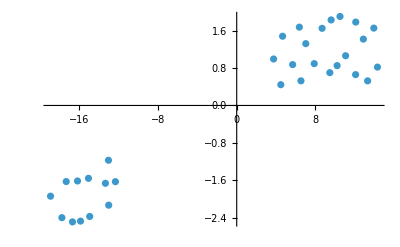

```mathematica
ListPlot[coordinatesAll]
```

```mathematica
coordinatesGen=DimensionReduce[DeleteDuplicates[allPossibleWords],2, FeatureExtractor->extractor, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesGen;
```

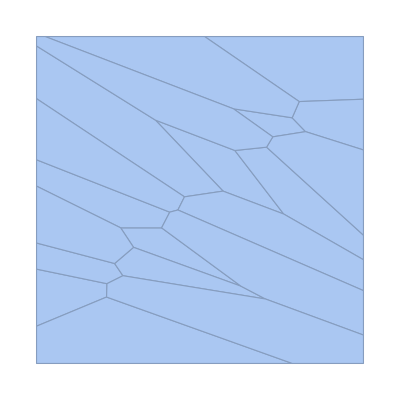

```mathematica
VoronoiMesh[coordinatesBase, AspectRatio->1]
```

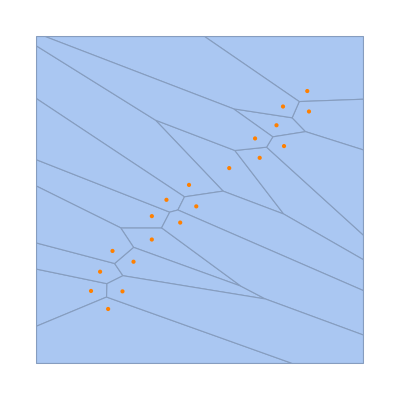

```mathematica
Show[%,Graphics[{Orange,Point[coordinatesBase]}, AspectRatio->1]]
```

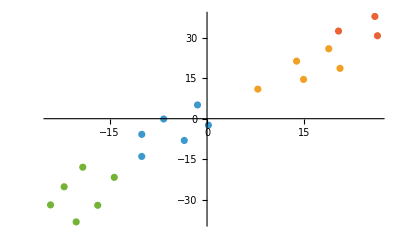

```mathematica
ListPlot[FindClusters[coordinatesBase,4,Method->"KMeans"]]
```

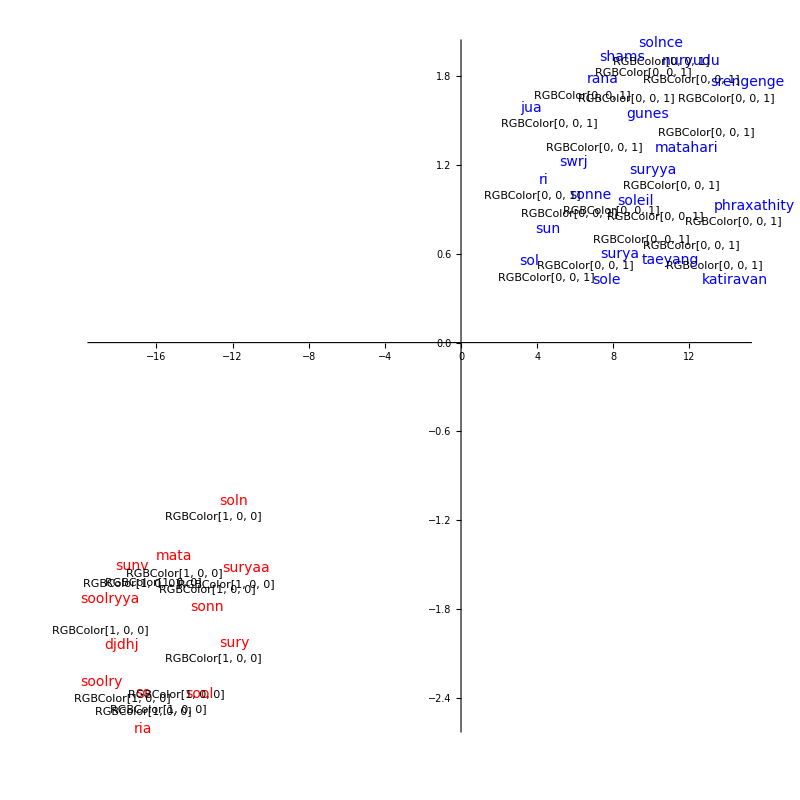

```mathematica
FeatureSpacePlot[
DeleteDuplicates[Join[
Labeled[#->Red, Style[#, Red, 14]]&/@allPossibleWords,
Labeled[#->Blue, Style[#, Blue, 14]]&/@translatedList
]],
FeatureExtractor->extractor,
LabelingSize->30,Axes->True, Method->"TSNE",ImageSize->{800,800}, AspectRatio->1
]
```

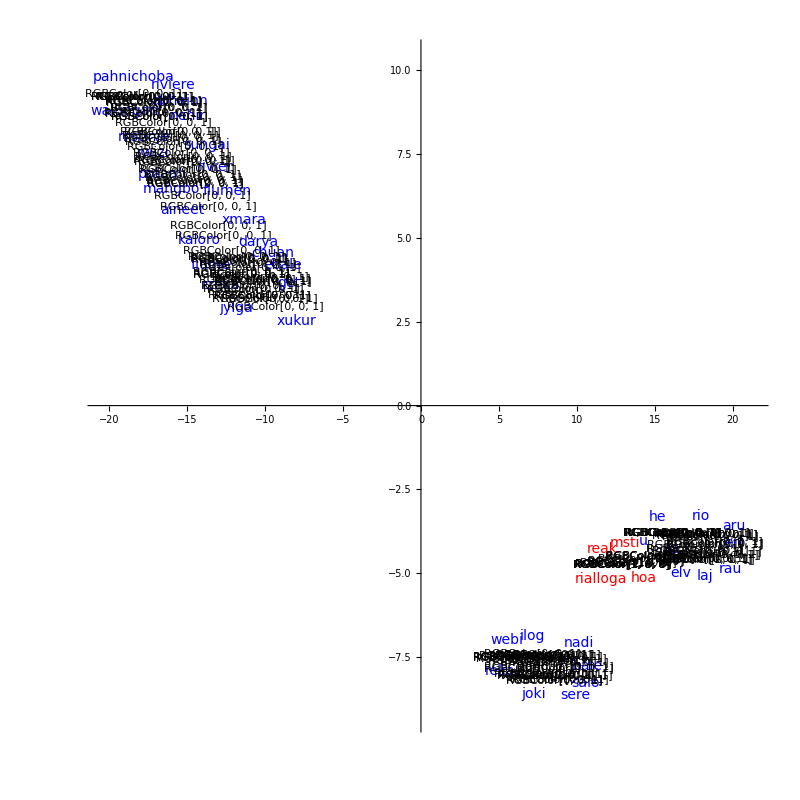

-Graphics-

## Metrics

We have some approaches which provide us with reasonable results. However, we need to quantify and visualize our newly generated words.

```mathematica
plotFitnessHeatmap[allPossibleWords_List]:=Module[{fitnessValues,reshapedValues,size,wordsMatrix},
	  fitnessValues=fitnessFunction /@ allPossibleWords;
	  size=Ceiling[Sqrt[Length[fitnessValues]]];
	  reshapedValues=PadRight[Partition[fitnessValues,size,size,{1,1},{}],{size,size},None];
	  wordsMatrix=PadRight[Partition[allPossibleWords,size,size,{1,1},""],{size,size},None];
	  ArrayPlot[reshapedValues,Color->"TemperatureMap",Frame->True,Mesh->True,MeshStyle->Gray,
	    PlotLabel->"Fitness Heatmap: Larger is better",ColorFunctionScaling->True,
	    Epilog->Flatten[
	      Table[
	        {
	          Text[Style[wordsMatrix[[i,j]],FontSize->12,Black],{j-0.5,size-i+0.25}],
	          Text[Style[NumberForm[reshapedValues[[i,j]],{4,2}],FontSize->12,Black],{j-0.5,size-i+0.75}]
	        },
	        {i,size},{j,size}
	      ]
	    ],
	    PlotLegends->BarLegend[{"TemperatureMap",{Min[fitnessValues],Max[fitnessValues]}}]
	  ]
	]
```

```mathematica
plotFitnessHeatmap[allPossibleWords]
```

plotFitnessHeatmap[{mata,ria,soln,sonn,sury,sunv,soolry,soolryya,sool,so,suryaa,djdhj}]

```mathematica
WordCloud[StringTake[allPossibleWords, 1]]
```

-Graphics-

```mathematica
plotFitnessHeatmap[allPossibleWords_List]:=Module[{fitnessValues,reshapedValues,size,wordsMatrix},
	  fitnessValues=extractor /@ allPossibleWords;
	  size=Ceiling[Sqrt[Length[fitnessValues]]];
	  reshapedValues=PadRight[Partition[fitnessValues,size,size,{1,1},{}],{size,size},None];
	  wordsMatrix=PadRight[Partition[allPossibleWords,size,size,{1,1},""],{size,size},None];
	  ArrayPlot[reshapedValues,ColorFunction->"TemperatureMap",Frame->True,Mesh->True,MeshStyle->Gray,
	    PlotLabel->"Neural Net Feature Extractor Heatmap: Smaller is better",ColorFunctionScaling->True,
	    Epilog->Flatten[
	      Table[
	        {
	          Text[Style[wordsMatrix[[i,j]],FontSize->12,Black],{j-0.5,size-i+0.25}],
	          Text[Style[NumberForm[reshapedValues[[i,j]],{4,2}],FontSize->12,Black],{j-0.5,size-i+0.75}]
	        },
	        {i,size},{j,size}
	      ]
	    ],
	    PlotLegends->BarLegend[{"TemperatureMap",{Min[fitnessValues],Max[fitnessValues]}}]
	  ]
	]
```